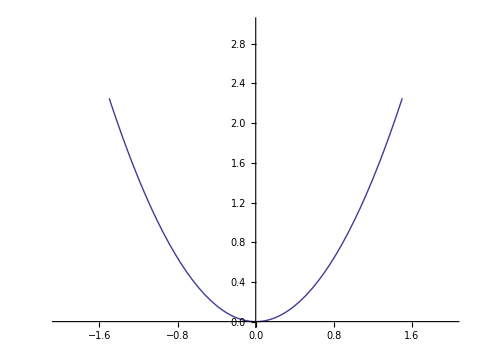

```mathematica
p1=Plot[x^2,{x,-1.5,1.5},AxesStyle->Arrowheads[0.03],PlotRange->{{-2,2},{0,3}},AspectRatio->3/4]
```

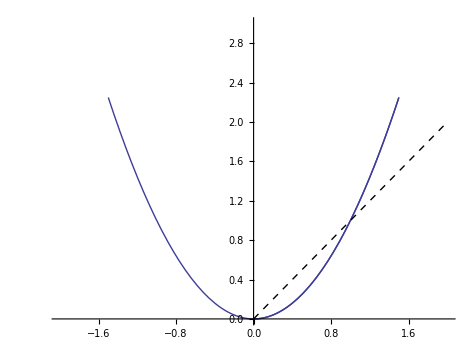

```mathematica
p2=Show[
Plot[x^2,{x,-1.5,1.5}],
Plot[x^2,{x,0,1.5},PlotStyle->{Thick}],
Plot[x,{x,0,2},PlotStyle->{Black,Dashed}],
PlotRange->{{-2,2},{0,3}},AspectRatio->3/4,AxesStyle->Arrowheads[0.03]
]
```

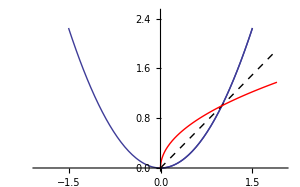

```mathematica
p3=Show[
Plot[x^2,{x,-1.5,1.5}],
Plot[x^2,{x,0,1.5},PlotStyle->{Thick}],
Plot[x,{x,0,1.9},PlotStyle->{Black,Dashed}],
Plot[Sqrt[x],{x,0,1.9},PlotStyle->{Red,Thick}],
PlotRange->{{-2,2},{0,2.5}},AspectRatio->2.5/4,AxesStyle->Arrowheads[0.03],ImageSize->300
]
```

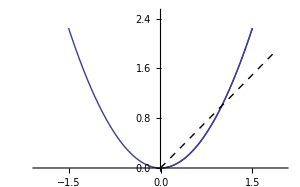

```mathematica
p2=Show[
Plot[x^2,{x,-1.5,1.5}],
Plot[x^2,{x,0,1.5},PlotStyle->{Thick}],
Plot[x,{x,0,1.9},PlotStyle->{Black,Dashed}],
PlotRange->{{-2,2},{0,2.5}},AspectRatio->2.5/4,AxesStyle->Arrowheads[0.03],ImageSize->300
]
```

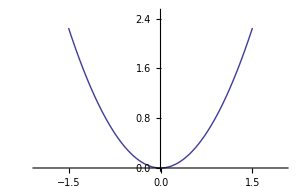

```mathematica
p1=Show[
Plot[x^2,{x,-1.5,1.5}],
PlotRange->{{-2,2},{0,2.5}},AspectRatio->2.5/4,AxesStyle->Arrowheads[0.03],ImageSize->300
]
```

```mathematica
Manipulate[{p1,p2,p3}[[i]],{i,1,3,1}]
```